```mathematica
Get["sac.m",Path->NotebookDirectory[]];
```

```mathematica
?sac`*
```

```mathematica
history=Simulate[500,20000];
```

```mathematica
effectiveHistory=Take[history,-10000];
```

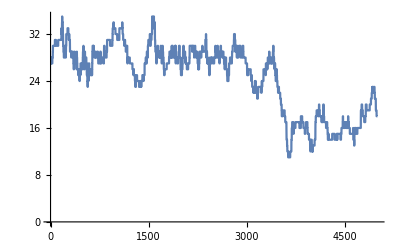

```mathematica
ListPlot[Unemployed[effectiveHistory],Joined->True,PlotRange->All]
```

```mathematica
firmHistories=FirmHistories[effectiveHistory];
```

```mathematica
firmProfitRates=FirmProfitRates[firmHistories];
```

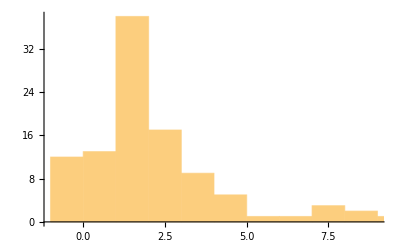
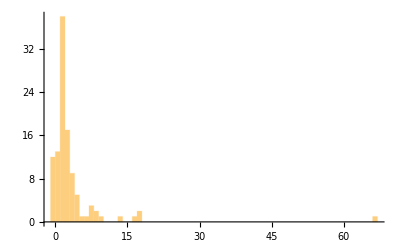

```mathematica
{Histogram[firmProfitRates],Histogram[firmProfitRates,PlotRange->All]}
```

```mathematica
firmSizes=FirmSizes[effectiveHistory];
```

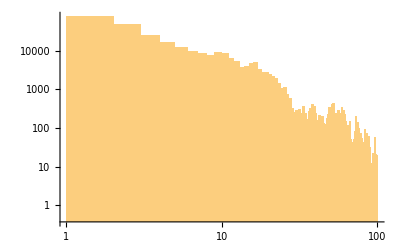

```mathematica
(* Should be a straight line *)
Histogram[firmSizes,PlotRange->All,ScalingFunctions->{"Log","Log"}]
```

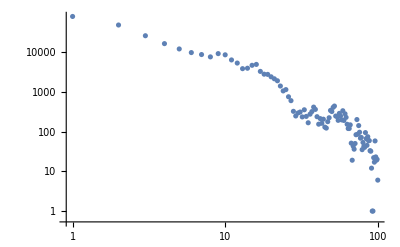

```mathematica
(* Should be a straight line *)
ListPlot[Drop[BinCounts[firmSizes],1],ScalingFunctions->{"Log","Log"},PlotRange->All]
```

```mathematica
EstimatedDistribution[firmSizes,ZipfDistribution[a,b]]
```

ZipfDistribution[100,0.361292]

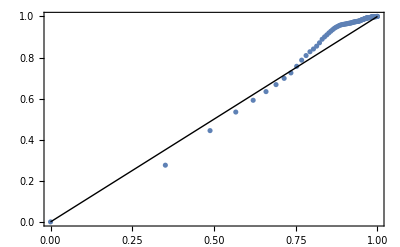

```mathematica
ProbabilityPlot[firmSizes,ZipfDistribution[a,b],PlotRange->All]
```

```mathematica
employeesMoney=EmployeesMoney[effectiveHistory];
```

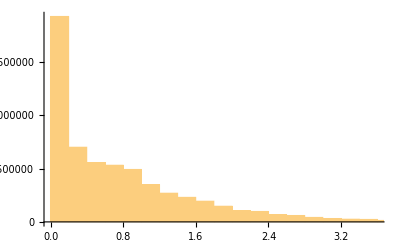

```mathematica
Histogram[employeesMoney]
```

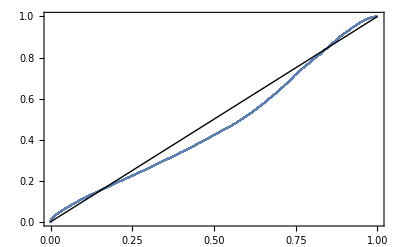

```mathematica
ProbabilityPlot[employeesMoney,GammaDistribution[a,b]]
```

```mathematica
(*workersWealth=WorkersWealth[history];*)
```

```mathematica
(*FindDistribution[workersWealth,TargetFunctions->"Continuous",MaxItems->1,PerformanceGoal->"Quality"]*)
```

```mathematica
(*FindDistributionParameters[workersWealth,ExponentialDistribution[a]]*)
```

```mathematica
(*ProbabilityPlot[workersWealth,GammaDistribution[a,b]]*)
```

```mathematica
employersWealth=EmployersWealth[effectiveHistory];
```

```mathematica
(* N.B. c=0 means location parameter is inoperative, and so reduces to ParetoDistribution[a,b] *)
EstimatedDistribution[employersWealth,ParetoDistribution[a,b,d]]
```

ParetoDistribution[4.56915,2.41289,7.9433×10^-6]

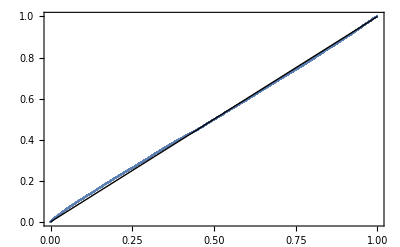

```mathematica
ProbabilityPlot[employersWealth,ParetoDistribution[a,b,d]]
```